```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/LISA_Fisher/math

## ρ*

```mathematica
Mpl=2.435 10^18;
c=299792458;
Mpcinm=3.086 10^16 10^6;
GeVinminv=10^9/(1.973 10^-7);
GeVinMpcinv=GeVinminv Mpcinm;
MpcinvinHz=c/Mpcinm;
```

```mathematica
w[ρ_]=1/3-σ/(ρ/ρs)Sqrt[π/2] E^(σ^2/2)(1/3-cs2min)Erfc[(σ^2-Log[ρ/ρs])/(Sqrt[2]σ)];
```

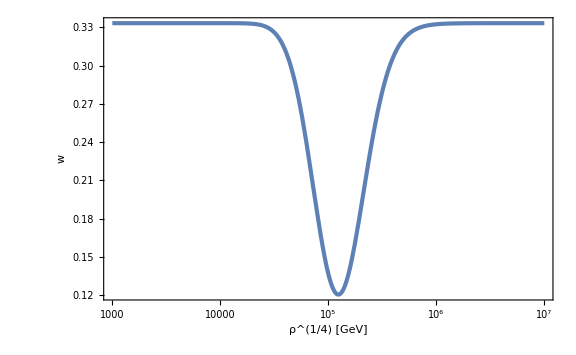

```mathematica
LogLinearPlot[w[ρquar^4]/.{ρs->10^(5 4),cs2min->0.1,σ->2},{ρquar,10^3,10^7},FrameLabel->{"ρ^(1/4) [GeV]",w}]
```

```mathematica
a1e4=1.927 10^-17;
η1e4=1.4 10^-11;
ηi=0;
```

```mathematica
bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(5 4),cs2min->0.1,σ->2},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
```

```mathematica
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
```

```mathematica
asol[η1e4]
```

1.927×10^-17

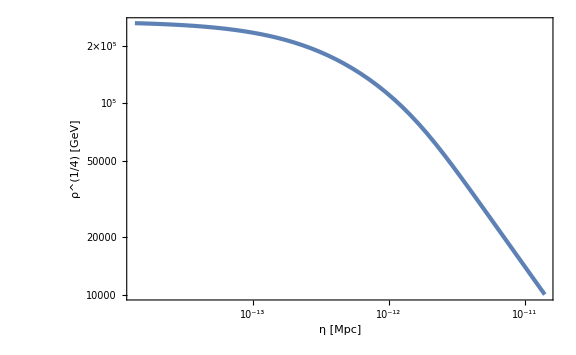

```mathematica
LogLogPlot[ρsol[η]^(1/4),{η,ηi,η1e4},FrameLabel->{"η [Mpc]","ρ^(1/4) [GeV]"},PlotRange->Full]
```

```mathematica
ks=ℋsol[η]/.FindRoot[ρsol[η]==10^(5 4),{η,10^-12},WorkingPrecision->30]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

6.59363×10^11

```mathematica
fs=10^3 ks/(2π)MpcinvinHz(*mHz*)
```

1.01946

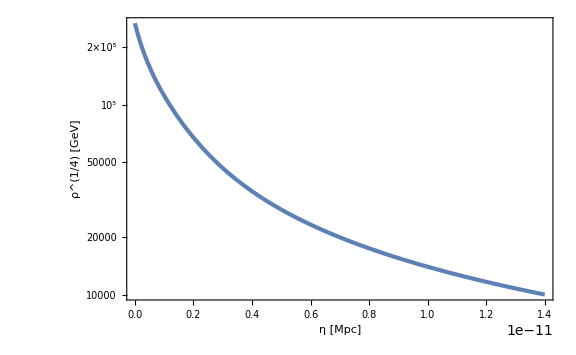

```mathematica
LogPlot[ρsol[η]^(1/4),{η,ηi,η1e4},FrameLabel->{"η [Mpc]","ρ^(1/4) [GeV]"},PlotRange->Full]
```

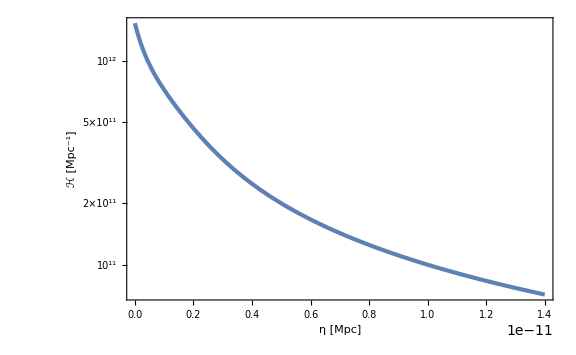

```mathematica
LogPlot[ℋsol[η],{η,ηi,η1e4},FrameLabel->{"η [Mpc]","ℋ [Mpc^-1]"},PlotRange->Full]
```

```mathematica
kscsList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(5 4),σ->2},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{cs2min,10^3 ℋsol[η]/(2π)MpcinvinHz/.FindRoot[ρsol[η]==10^(5 4),{η,10^-12},WorkingPrecision->30]//Quiet},{cs2min,0.09,0.11,10^-3}];
```

```mathematica
kscsfit[x_]=a(x-0.1)+fs/.FindFit[kscsList,a(x-0.1)+fs,a,x]
```

1.01946+0.389821 (-0.1+x)

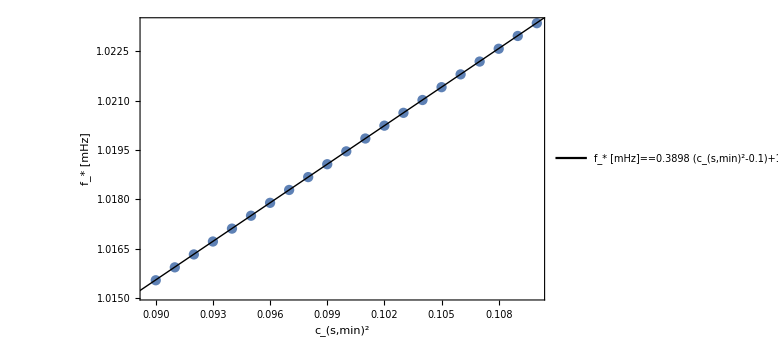

```mathematica
Show[ListPlot[kscsList,Joined->False,FrameLabel->{{"f_* [mHz]",None},{Subscript["c", "s",min]^2,Row[{Superscript[SubStar[ρ],"1/4"]=="100 TeV",",   ",σ==2}]}}],
Plot[kscsfit[x],{x,0.08,0.12},PlotStyle->{Black,Thin},PlotLegends->Placed[LineLegend[{"f_* [mHz]"==0.3898(Subscript["c", "s",min]^2-0.1)+1.019},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.65,0.15}]]]
```

```mathematica
kssigmaList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(5 4),cs2min->0.1},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{σ,10^3 ℋsol[η]/(2π)MpcinvinHz/.FindRoot[ρsol[η]==10^(5 4),{η,10^-12},WorkingPrecision->30]//Quiet},{σ,1.9,2.1,10^-2}];
```

```mathematica
kssigmafit[x_]=a(x-2)+fs/.FindFit[kssigmaList,a(x-2)+fs,a,x]
```

1.01946-0.0578986 (-2+x)

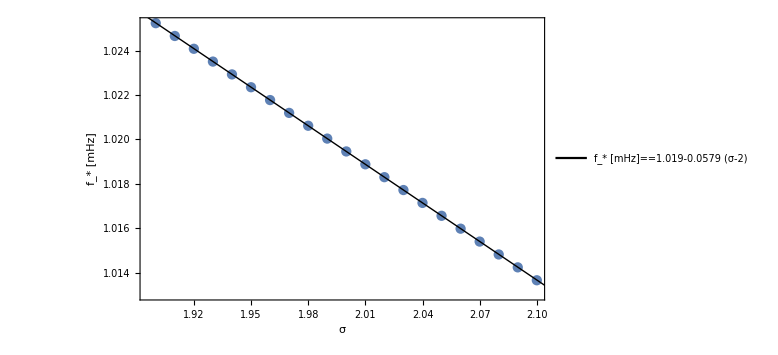

```mathematica
Show[ListPlot[kssigmaList,Joined->False,FrameLabel->{{"f_* [mHz]",None},{σ,Row[{Superscript[SubStar[ρ],"1/4"]=="100 TeV",",   ",Subscript["c", "s",min]^2==0.1}]}}],
Plot[kssigmafit[x],{x,1.8,2.2},PlotStyle->{Black,Thin},PlotLegends->Placed[LineLegend[{"f_* [mHz]"==-0.0579(σ-2)+1.019},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.35,0.15}]]]
```

```mathematica
lnkslnρsList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(4lnρsQ),σ->2,cs2min->0.1},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{lnρsQ,Log10[10^3 ℋsol[η]/(2π)MpcinvinHz]/.FindRoot[ρsol[η]==10^(4lnρsQ),{η,10^-12},WorkingPrecision->30]//Quiet},{lnρsQ,4.9,5.1,10^-2}];
```

```mathematica
ksρsfit[x_]=fs 10^(a(Log10[x]-5))/.FindFit[lnkslnρsList,a(x-5)+Log10[fs],a,x]
```

1.01946 10^(0.999998 (-5+Log[x]/Log[10]))

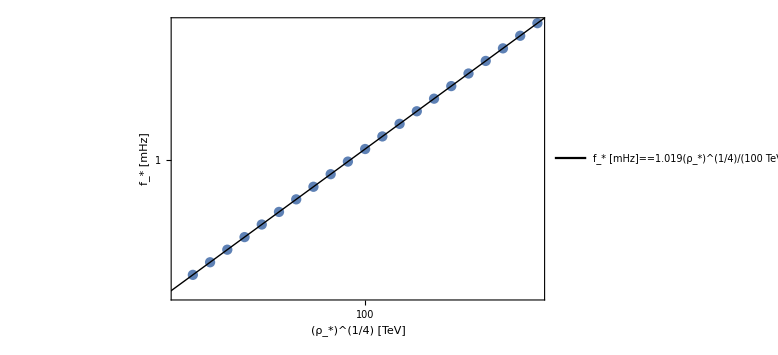

```mathematica
Show[ListLogLogPlot[Map[{10^(#[[1]]-3),10^(#[[2]])}&,lnkslnρsList],Joined->False,FrameLabel->{{"f_* [mHz]",None},{"(ρ_*)^(1/4) [TeV]",Row[{Subscript["c", "s",min]^2==0.1,",   ",σ==2}]}}],
LogLogPlot[ksρsfit[x 10^3],{x,10^1.8,10^2.2},PlotStyle->{Black,Thin},PlotLegends->Placed[LineLegend[{"f_* [mHz]"==Row[{1.019,(Superscript[SubStar[ρ],"1/4"]/("100 TeV"))}]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.65,0.15}]]]
```

```mathematica
ksρscsmList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(4lnρsQ),σ->2,cs2min->0.09},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{10^(lnρsQ-3),10^3 ℋsol[η]/(2π)MpcinvinHz/.FindRoot[ρsol[η]==10^(4lnρsQ),{η,10^-12},WorkingPrecision->30]//Quiet},{lnρsQ,4.9,5.1,10^-2}];
```

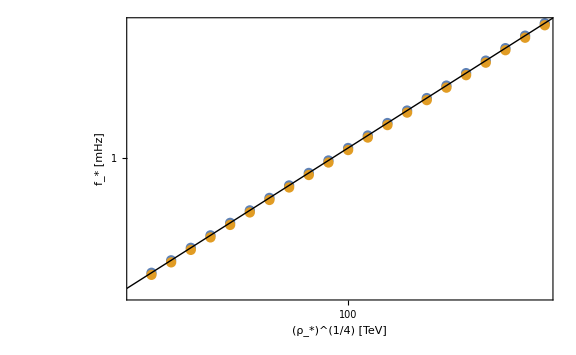

```mathematica
Show[ListLogLogPlot[{Map[{10^(#[[1]]-3),10^(#[[2]])}&,lnkslnρsList],ksρscsmList},Joined->False,FrameLabel->{{"f_* [mHz]",None},{"(ρ_*)^(1/4) [TeV]",Row[{Subscript["c", s,min]^2==0.1,",   ",σ==2}]}}],
LogLogPlot[ksρsfit[x 10^3],{x,10^1.8,10^2.2},PlotStyle->{Black,Thin}]]
```

## Fisher

```mathematica
$Assumptions={A>0};
```

```mathematica
MIDNIGHT=RGBColor["#2C3E50"]
```

RGBColor[0.17254901960784313, 0.24313725490196078, 0.3137254901960784]

```mathematica
GWList=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=0.000e+00.dat"];
GWListcsp=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.100e-01_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=1.000e-02_deltasigma=0.000e+00.dat"];
GWListcsm=Import["dataIGWS_17012024/17012024gws_julia_csmin=9.000e-02_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=-1.000e-02_deltasigma=0.000e+00.dat"];
GWListsp=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=2.100e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=1.000e-01.dat"];
GWListsm=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=1.900e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=-1.000e-01.dat"];
```

```mathematica
dcs=0.01;
ds=0.1;
```

```mathematica
GWint[f_]=Interpolation[GWList][f];
GWintcsp[f_]=Interpolation[GWListcsp][f];
GWintcsm[f_]=Interpolation[GWListcsm][f];
GWintsp[f_]=Interpolation[GWListsp][f];
GWintsm[f_]=Interpolation[GWListsm][f];
```

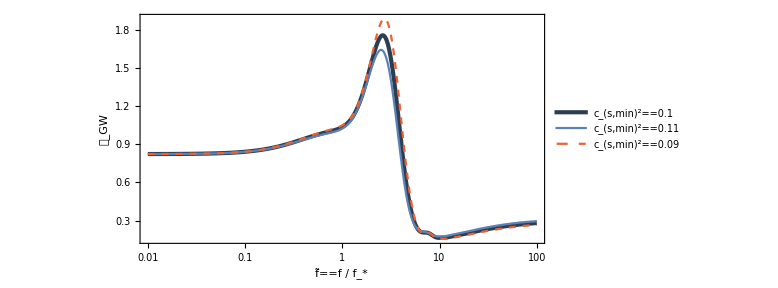

```mathematica
LogLinearPlot[{GWint[f],GWintcsp[f],GWintcsm[f]},{f,10^-2,10^2},FrameLabel->{{Subscript[𝒯, GW],None},{OverTilde[f]=="f / f_*",σ==2}},PlotStyle->{{AbsoluteThickness[3],MIDNIGHT},{Color[1]},{Color[4],Dashed}},PlotLegends->Placed[LineLegend[{Subscript[c, "s,min"]^2==0.1,Subscript[c, "s,min"]^2==0.11,Subscript[c, "s,min"]^2==0.09},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.2,0.75}],AspectRatio->1/2]
```

```mathematica
FindMaximum[GWint[f],{f,2}]
```

{1.75734,{f→2.60395}}

```mathematica
GWintcsp[3.45]-GWintcsm[3.45]
```

-0.369879

```mathematica
GWintcsp[2.6]-GWintcsm[2.6]
```

-0.24205

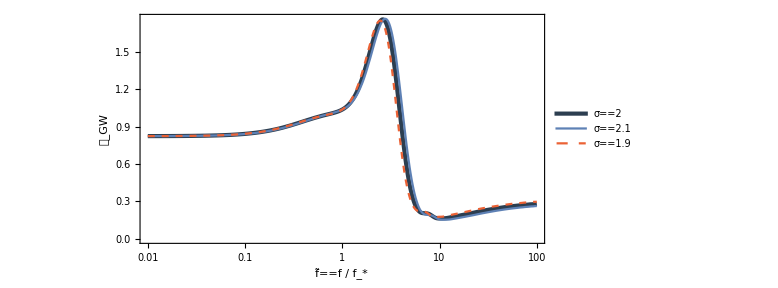

```mathematica
LogLinearPlot[{GWint[f],GWintsp[f],GWintsm[f]},{f,10^-2,10^2},FrameLabel->{{Subscript[𝒯, GW],None},{OverTilde[f]=="f / f_*",Subscript[c, "s,min"]^2==0.1}},PlotStyle->{{AbsoluteThickness[3],MIDNIGHT},{Color[1]},{Color[4],Dashed}},PlotLegends->Placed[LineLegend[{σ==2,σ==2.1,σ==1.9},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.2,0.75}],AspectRatio->1/2]
```

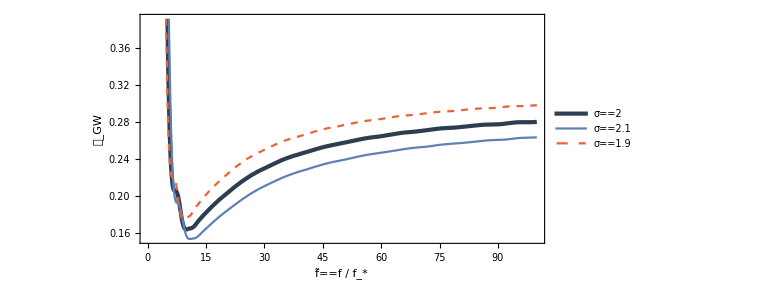

```mathematica
Plot[{GWint[f],GWintsp[f],GWintsm[f]},{f,10^-2,10^2},FrameLabel->{{Subscript[𝒯, GW],None},{OverTilde[f]=="f / f_*",Subscript[c, "s,min"]^2==0.1}},PlotStyle->{{AbsoluteThickness[3],MIDNIGHT},{Color[1]},{Color[4],Dashed}},PlotLegends->Placed[LineLegend[{σ==2,σ==2.1,σ==1.9},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.2,0.75}],AspectRatio->1/2]
```

```mathematica
dGWdcs[f_]=(GWintcsp[f]-GWintcsm[f])/(2dcs);
dGWds[f_]=(GWintsp[f]-GWintsm[f])/(2ds);
```

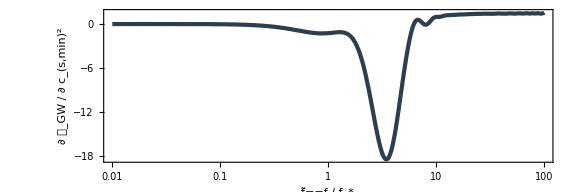

```mathematica
LogLinearPlot[dGWdcs[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*",Row[{"∂ 𝒯_GW / ∂ ", Subscript[c, "s,min"]^2}]},PlotStyle->{AbsoluteThickness[3],MIDNIGHT}]
```

```mathematica
FindMinimum[dGWdcs[f],{f,3}]
```

{-18.494,{f→3.45023}}

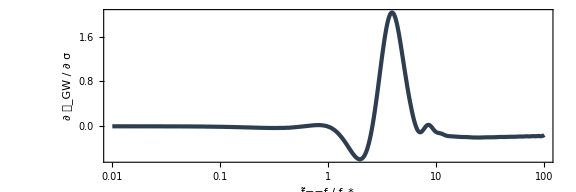

```mathematica
LogLinearPlot[dGWds[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*","∂ 𝒯_GW / ∂ σ"},PlotStyle->{AbsoluteThickness[3],MIDNIGHT}]
```

```mathematica
L=2.5 10^9(*m*);
Tobs=4 60 60 24 365(*s*)
fs=10^-3(*s^-1*);
Ωrh2=4.2 10^-5;
c=299792458(*m/s*);
pc=3.086 10^16(*m*);
Hnorm=(100 10^3)/(10^6 pc)(*s*)
fmax=10^2;
fmin=10^-3;
```

126144000

3.24044×10^-18

```mathematica
RAA[f_]=9/20 1/(1+0.7((2π f L)/c)^2);
REE[f_]=RAA[f];
RTT[f_]=9/20((2π f L)/c)^6/(1.8 10^3+0.7((2π f L)/c)^8);
```

```mathematica
calRAA[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RAA[f];
calREE[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 REE[f];
calRTT[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RTT[f];
```

```mathematica
PIMS[f_]=P^2 10^(-12 2)(1+((2 10^-3)/f)^4)((2π f)/c)^2/.{P->15}(*s*);
Pacc[f_]=A^2 10^(-15 2)(1+((0.4 10^-3)/f)^2)(1+(f/(8 10^-3))^4)(1/(2π f))^4((2π f)/c)^2/.{A->3}(*s*);
```

```mathematica
NAA[f_]=8 Sin[(2π f L)/c]^2(4(1+Cos[(2π f L)/c]+Cos[(2π f L)/c]^2)Pacc[f]+(2+Cos[(2π f L)/c])PIMS[f]);
NEE[f_]=NAA[f];
NTT[f_]=16 Sin[(2π f L)/c]^2(1(1-Cos[(2π f L)/c])^2 Pacc[f]+(1-Cos[(2π f L)/c])PIMS[f]);
```

```mathematica
SnAA[f_]=NAA[f]/calRAA[f];
SnEE[f_]=NEE[f]/calREE[f];
SnTT[f_]=NTT[f]/calRTT[f];
```

```mathematica
ΩnAAh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnAA[f];
ΩnEEh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnEE[f];
ΩnTTh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnTT[f];
```

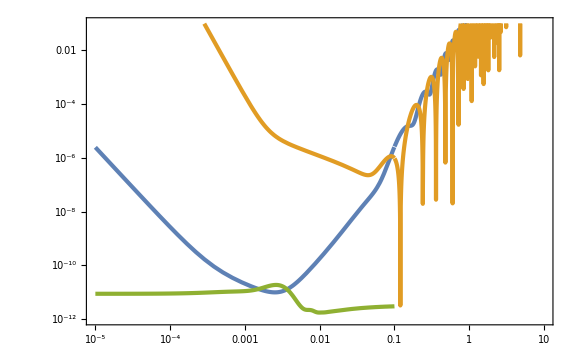

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 (5 10^-4)^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},PlotRange->{10^-12,10^-1}]
```

```mathematica
As=10^-5;
```

```mathematica
1/2 Tobs Ωrh2^2 As^4
```

1.11259×10^-21

```mathematica
(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)/.{f->0.003}
```

83.8306

```mathematica
NIntegrate[(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}]
NIntegrate[E^lnf((dGWds[E^lnf/fs]dGWds[E^lnf/fs])/((10^10 ΩnAAh2[E^lnf])^2)+(dGWds[E^lnf/fs]dGWds[E^lnf/fs])/((10^10 ΩnEEh2[E^lnf])^2)+(dGWds[E^lnf/fs]dGWds[E^lnf/fs])/((10^10 ΩnTTh2[E^lnf])^2)),{lnf,Log[fs fmin],Log[fs fmax]}]
```

0.648986

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in lnf near {lnf} = {-5.51829}. NIntegrate obtained 0.648986 and 9.25421×10^-7 for the integral and error estimates.

0.648986

```mathematica
fs fmin
fs fmax
```

1/1000000

1/10

```mathematica
Fisher[A_]=0.11(A/As)^4{{NIntegrate[(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWds[f/fs]dGWds[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}],NIntegrate[(dGWds[f/fs]dGWdcs[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWds[f/fs]dGWdcs[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWds[f/fs]dGWdcs[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}]},{NIntegrate[(dGWdcs[f/fs]dGWds[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWdcs[f/fs]dGWds[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWdcs[f/fs]dGWds[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}],NIntegrate[(dGWdcs[f/fs]dGWdcs[f/fs])/((10^10 ΩnAAh2[f])^2)+(dGWdcs[f/fs]dGWdcs[f/fs])/((10^10 ΩnEEh2[f])^2)+(dGWdcs[f/fs]dGWdcs[f/fs])/((10^10 ΩnTTh2[f])^2),{f,fs fmin,fs fmax}]}}
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in f near {f} = {0.00342667}. NIntegrate obtained -5.66897 and 0.000112894 for the integral and error estimates.

{{7.13885×10^18 A^4,-6.23586×10^19 A^4},{-6.23586×10^19 A^4,8.89939×10^20 A^4}}

```mathematica
CovC[A_]=Inverse[Fisher[A]]
```

{{(3.61097×10^-19)/A^4,(2.53023×10^-20)/A^4},{(2.53023×10^-20)/A^4,(2.89662×10^-21)/A^4}}

```mathematica
a[A_]=Sqrt[(CovC[A][[1,1]]+CovC[A][[2,2]])/2+Sqrt[(CovC[A][[1,1]]-CovC[A][[2,2]])^2/4+(CovC[A][[1,2]])^2]]//Simplify
b[A_]=Sqrt[(CovC[A][[1,1]]+CovC[A][[2,2]])/2-Sqrt[(CovC[A][[1,1]]-CovC[A][[2,2]])^2/4+(CovC[A][[1,2]])^2]]//Simplify
θ[A_]=ArcTan[(2CovC[A][[1,2]])/(CovC[A][[1,1]]-CovC[A][[2,2]])]/2//Simplify
```

(6.02392×10^-10)/A^2

(3.3439×10^-11)/A^2

0.0701729

```mathematica
α1=1.52;
α2=2.48;
```

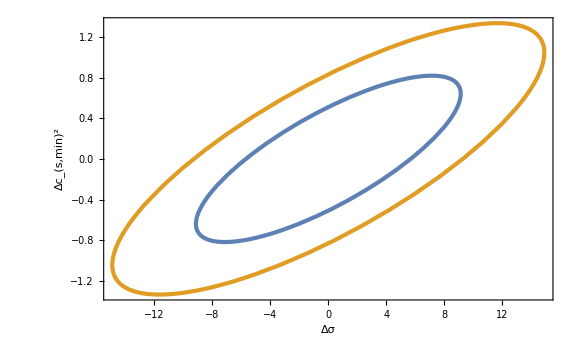

```mathematica
ParametricPlot[{α1 RotationMatrix[θ[As]].{a[As]Cos[t],b[As]Sin[t]},α2 RotationMatrix[θ[As]].{a[As]Cos[t],b[As]Sin[t]}},{t,0,2π},FrameLabel->{{Subscript[Δc, s,min]^2,None},{Δσ,Subscript[A, "s"]=="10^-5"}}]
```

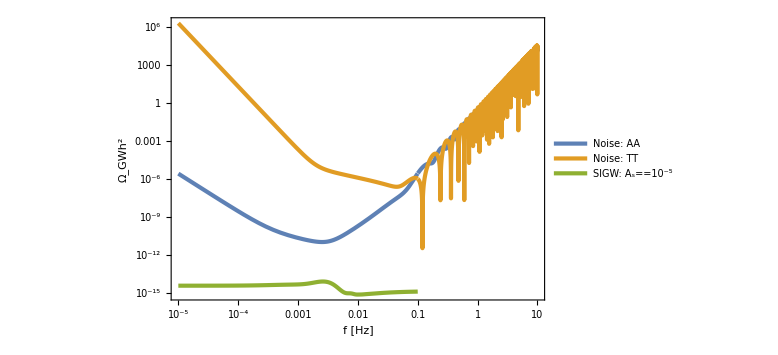

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 As^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},FrameLabel->{"f [Hz]","Ω_GWh^2"},PlotLegends->Placed[LineLegend[{"Noise: AA","Noise: TT",Row[{"SIGW: ",Subscript[A, "s"]=="10^-5"}]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.55,0.8}]]
```